-Graphics-   -Graphics-

```mathematica
n=6;m=4;
```

```mathematica
suits={Style["♣",FontSize->22],Style["♢",Red,FontSize->22],Style["♡",Red,FontSize->22],Style["♠",FontSize->22]};
```

```mathematica
nas[L_]:=(Length[Union[Extract[A,L]]]<4)
```

```mathematica
(*don't use*)
initialize:=(A=Table[0,{n},{n}];
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
A=ReplacePart[A,{i,j}->Which[i==1&&j==1,r[{}],i==1,r[{A[[i,j-1]]}],j==1,r[{A[[i-1,j]]}],True,r[{A[[i-1,j]],A[[i,j-1]]}]]]]];)
```

```mathematica
initialize:=(A=Table[RandomInteger[{1,4}],{n},{m}];)
```

```mathematica
r[L_]:=(e=RandomInteger[{1,4}];While[MemberQ[L,e],e=RandomInteger[{1,4}]];e)
```

```mathematica
beforepic[A_]:=Graphics[{
MapIndexed[Text[suits[[#1]],#2-{1/2,1/2}]&,A,{2}],
Style[{Table[Line[{{0,i},{n,i}}],{i,0,m}],Table[Line[{{i,0},{i,m}}],{i,0,n}]
},Antialiasing->False]
},ImageSize->{1+20n,1+20m},PlotRange->{{0,n},{0,m}}]
```

```mathematica
afterpic[A_,L_]:=Graphics[{
MapIndexed[Text[suits[[#1]],#2-{1/2,1/2}]&,A,{2}],
Style[{Table[Line[{{0,i},{n,i}}],{i,0,m}],Table[Line[{{i,0},{i,m}}],{i,0,n}],AbsoluteThickness[2],Hue[1/3,1,.8],Line[Map[#-{1/2,1/2}&,L~Join~{First[L]}]]
},Antialiasing->False]
},ImageSize->{1+20n,1+20m},PlotRange->{{0,n},{0,m}}]
```

```mathematica
initialize;beforepic[A]
```

-Graphics-

```mathematica
n=8;m=5;
For[k=1,k>0,k++,
initialize;
While[Min[Table[Count[Flatten[A],i],{i,1,4}]]<n m/5,initialize];
stac={{{1,1},{1,2}}};
solns={};
While[Length[stac]>0&&Length[solns]<2,
cur=First[stac];
stac=Rest[stac];
last=Last[cur];
If[Length[cur]==n m&&last=={2,1}&&nas[Take[cur,-3]~Join~Take[cur,1]]&&nas[Take[cur,-2]~Join~Take[cur,2]]&&nas[Take[cur,-1]~Join~Take[cur,3]],AppendTo[solns,cur]];
poss=Select[Map[last+#&,{{0,1},{1,0},{0,-1},{-1,0}}],1≤#[[1]]≤n&&1≤#[[2]]≤m&&Not[MemberQ[cur,#]]&];
If[Length[cur]≥3, poss=Select[poss,nas[Take[cur,-3]~Join~{#}]&]];
stac=Map[Append[cur,#]&,poss]~Join~stac];
Print[Length[solns]];
If[Length[solns]==1,Print[beforepic[A],"   ",afterpic[A,solns[[1]]]]]]
```

## 4x4

-Graphics-   -Graphics-

-Graphics-   -Graphics-

-Graphics-   -Graphics-

«8 more identical outputs»

## 5x4

-Graphics-   -Graphics-

-Graphics-   -Graphics-

-Graphics-   -Graphics-

«1 more identical outputs»

## 6x4

-Graphics-   -Graphics-

-Graphics-   -Graphics-

-Graphics-   -Graphics-

«5 more identical outputs»

## 6x5

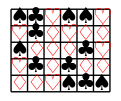
-Graphics-   -Graphics-

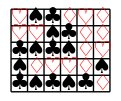
-Graphics-   -Graphics-

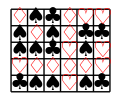
-Graphics-   -Graphics-

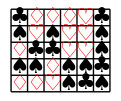
-Graphics-   -Graphics-

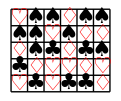
-Graphics-   -Graphics-

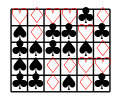
-Graphics-   -Graphics-

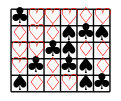
-Graphics-   -Graphics-

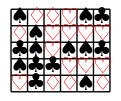
-Graphics-   -Graphics-

## 6x6

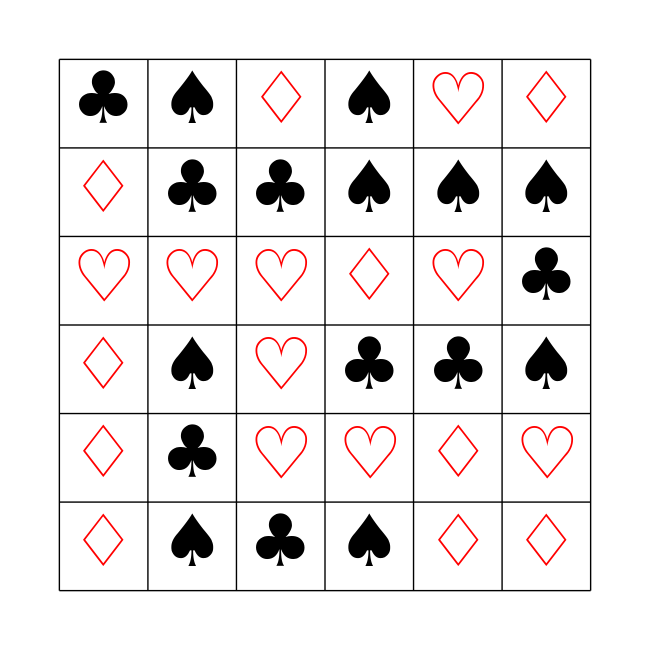
-Graphics-     -Graphics-

-Graphics-   -Graphics-

-Graphics-   -Graphics-

-Graphics-   -Graphics-

«8 more identical outputs»